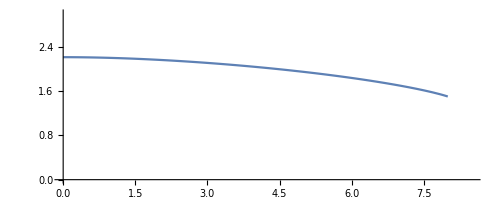

```mathematica
ν=0.03;
ϵ=0.002;
thickness=1.5;
radius=8;
start= 0.000000000001;

eq1=ρ/1 D[ρ((D[r2[ρ],ρ])+(ν r2[ρ])/1+1/2 ρ(D[z1[ρ], ρ])^2), ρ]-ν/1 ρ(D[r2[ρ],ρ]+1/2(D[z1[ρ], ρ])^2)-r2[ρ]/1==0;
eq2=1/1 D[1(D[z1[ρ], ρ])(D[r2[ρ],ρ]ρ+ν r2[ρ]/1+1/2(D[z1[ρ], ρ])^2 ρ), ρ]==-ρ;
s=NDSolve[{eq1, eq2, r2[1]==0,z1[1]==0,(D[z1[ρ], ρ]/.ρ->0)==0 , r2[start]==0},{r2, z1},{ρ,start,1}];
(*simplethickness plot*)
expr0 = {radius*(ρ+ϵ^(2/3) r2[ρ]),radius*(ϵ^(1/3)z1[ρ])+thickness};
ParametricPlot[{Evaluate[expr0/.s]}, {ρ, start, 1}, PlotRange->{{0, 8.5},{0, 3}}]


(*ParametricPlot[{Evaluate[{radius*(1+ϵ^(2/3)r2'[ρ]),radius*(ϵ^(1/3)z1'[ρ])}/.s]}, {ρ, start, 1}, PlotRange->Full]*)
(*ParametricPlot[Evaluate[r2[ρ], z1[ρ]]/.s, {ρ, 0.1, 1}]*)
```

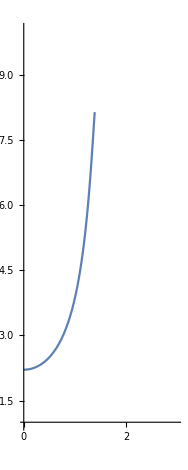

```mathematica
(*thickness as a function of angle from normal*)
expr1 = {ArcTan[radius*(ρ+ϵ^(2/3) r2[ρ])/(radius*(ϵ^(1/3)z1[ρ])+thickness)],√((radius*(ρ+ϵ^(2/3) r2[ρ]))^2+(radius*(ϵ^(1/3)z1[ρ])+thickness)^2)};
ParametricPlot[{Evaluate[expr1/.s]}, {ρ, start, 1}, PlotRange->{{0, 3},{1,10 }}]
Export["thickness.txt",Table[Evaluate[expr1/.s], {ρ, start, 2.0, 0.001}]]
```

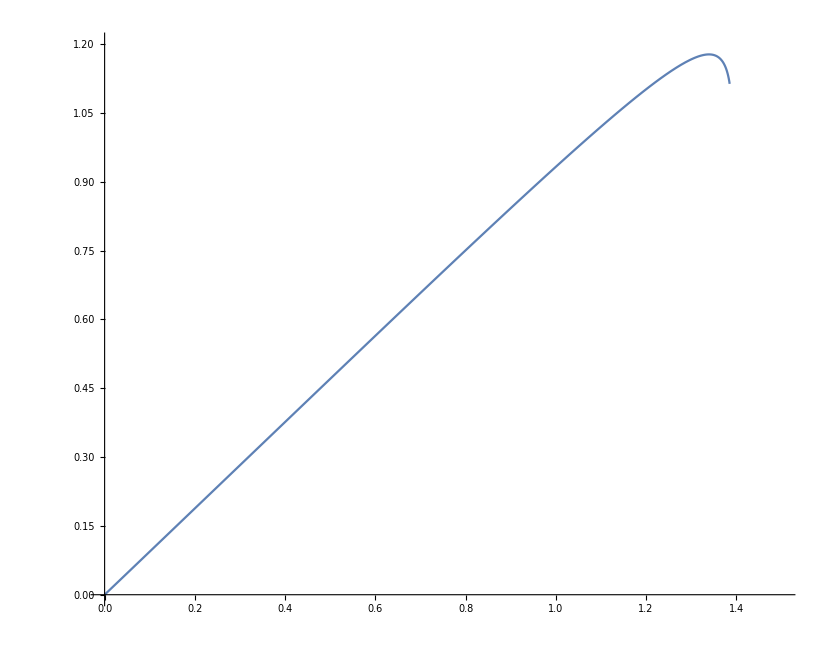

```mathematica
(*havar entrance angle as a function of angle from normal*)
expr2 = {ArcTan[radius*(ρ+ϵ^(2/3) r2[ρ])/(radius*(ϵ^(1/3)z1[ρ])+thickness)],π/2-ArcCos[((radius*(ρ+ϵ^(2/3) r2[ρ])*radius*(1+ϵ^(2/3) D[r2[ρ], ρ])+(radius*(ϵ^(1/3)z1[ρ])+thickness)*radius*(ϵ^(1/3)D[z1[ρ], ρ]))/(√((radius*(ρ+ϵ^(2/3) r2[ρ]))^2+(radius*(ϵ^(1/3)z1[ρ])+thickness)^2)*√((radius*(1+ϵ^(2/3) D[r2[ρ], ρ]))^2+(radius*(ϵ^(1/3)D[z1[ρ], ρ]))^2)))]};
ParametricPlot[{Evaluate[expr2/.s]}, {ρ, start, 1}, PlotRange->{{0, 1.5},{0,1.2}}]
Table[Evaluate[expr2/.s], {ρ, start, 1.5, 0.001}]
```